# Semantic Similarity Networks

## Rijksmuseum Semantic Explorer — Notebook 2 of 5

Embedding vectors define a continuous space, but graph structures can reveal discrete community structure that is hard to see in a scatter plot. This notebook constructs a k-nearest-neighbor graph where each artwork is a vertex and edges connect it to its k most semantically similar neighbors. We then apply graph-theoretic tools — community detection, centrality measures, degree analysis — to discover the large-scale organisation of the Rijksmuseum collection. The resulting communities often align with, but sometimes cut across, traditional art-historical categories, revealing unexpected semantic connections between artworks.

## 1. Data Loading

```mathematica
dataDir = FileNameJoin[{NotebookDirectory[], "data"}];
If[!DirectoryQ[dataDir],
  Print["Data not found. Run: uv run python export_for_mathematica.py"];
  Abort[]];
manifest = Import[FileNameJoin[{dataDir, "metadata.json"}], "RawJSON"];
{n, dim} = Lookup[manifest, {"n", "dim"}];
raw = BinaryReadList[FileNameJoin[{dataDir, "embeddings.bin"}], "Real32"];
embeddings = Partition[raw, dim];
artIds = manifest["art_ids"];
artworks = manifest["artworks"];
Print["Loaded ", n, " embeddings"]
```

Loaded 20000 embeddings

## 2. Similarity Matrix

Computing a full pairwise similarity matrix for all 20,000 artworks would require 400 million entries, which is memory-intensive. Instead, we randomly subsample 2,000 artworks, giving a manageable 2K×2K matrix. Because the embeddings are L2-normalised, cosine similarity between any two vectors is simply their dot product, so the entire similarity matrix is computed via a single matrix multiplication — one of the most highly optimised operations in numerical computing. Sorting the matrix by object type before plotting reveals block-diagonal structure corresponding to type-based clusters.

```mathematica
graphN = Min[n, 2000];
SeedRandom[42];
graphIdx = RandomSample[Range[n], graphN];
graphEmb = embeddings[[graphIdx]];
graphIds = artIds[[graphIdx]];

(* Cosine similarity matrix via matrix multiply *)
simMat = graphEmb.Transpose[graphEmb];
(* Zero out self-similarities *)
Do[simMat[[i, i]] = 0, {i, graphN}];
Print["Similarity matrix: ", Dimensions[simMat]]
```

Similarity matrix: {2000,2000}

```mathematica
(* Visualize similarity matrix (sorted by primary type for structure) *)
graphTypes = Table[
  Module[{types = artworks[ToString[id]]["types"]},
    If[Length[types] > 0, First[types], "zzz_unknown"]],
  {id, graphIds}];
typeOrder = Ordering[graphTypes];

MatrixPlot[simMat[[typeOrder, typeOrder]],
  PlotLabel -> "Cosine Similarity Matrix (sorted by type)",
  ColorFunction -> "TemperatureMap",
  MaxPlotPoints -> 500,
  ImageSize -> 500]
```

-Graphics-

## 3. k-NN Graph Construction

The full similarity matrix is dense — every artwork has some nonzero similarity to every other. To extract meaningful structure, we sparsify it into a k-nearest-neighbor graph: for each artwork, we keep only the top k=8 most similar connections. This choice of k balances detail against noise: too small and the graph fragments into disconnected components; too large and community structure is washed out. We symmetrise the directed k-NN edges into undirected edges. The resulting graph's basic properties — whether it is connected and how many components it has — already tell us something about the embedding space topology.

```mathematica
k = 8;
edges = Flatten[Table[
  Module[{topK = Ordering[simMat[[i]], -k]},
    UndirectedEdge[i, #] & /@ topK],
  {i, graphN}]];
edges = DeleteDuplicates[Sort /@ edges];

g = Graph[Range[graphN], edges,
  GraphLayout -> "SpringElectricalEmbedding",
  VertexSize -> 0.3,
  EdgeStyle -> Directive[Opacity[0.05], Gray]];
Print["Graph: ", VertexCount[g], " vertices, ", EdgeCount[g], " edges"]
Print["Connected: ", ConnectedGraphQ[g]]
Print["Components: ", Length[ConnectedComponents[g]]]
```

Graph: 2000 vertices, 13207 edges

Connected: True

Components: 1

## 4. Community Detection

Community detection algorithms partition the graph into groups of densely interconnected vertices with sparser connections between groups. FindGraphCommunities uses modularity optimisation, which maximises the difference between actual intra-community edge density and the density expected under a random null model. The discovered communities represent semantic clusters — groups of artworks that are collectively more similar to each other than to the rest of the collection. The CommunityGraphPlot arranges communities spatially and draws boundaries around them, giving an intuitive map of the collection's semantic landscape. The size distribution reveals whether the collection is dominated by a few large clusters or fragmented into many small ones.

```mathematica
communities = FindGraphCommunities[g];
Print["Found ", Length[communities], " communities"]
commSizes = Reverse[Sort[Length /@ communities]];
Print["Largest 10: ", commSizes[[1 ;; Min[10, Length[commSizes]]]]]

(* Community graph plot *)
CommunityGraphPlot[g, communities,
  CommunityBoundaryStyle -> Directive[Opacity[0.4], Gray, Dashed],
  PlotLabel -> "Semantic Communities (k=" <> ToString[k] <> " NN graph)",
  VertexSize -> 0.3,
  EdgeStyle -> Directive[Opacity[0.03], Gray],
  ImageSize -> 800]
```

Found 8 communities

Largest 10: {601,566,487,226,50,32,28,10}

-Graphics-

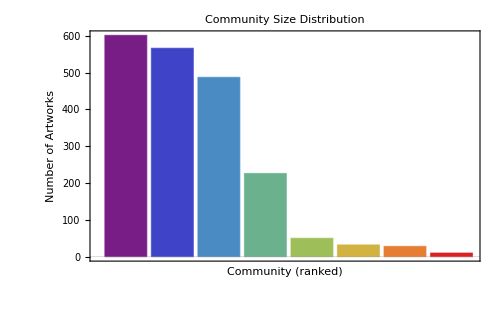

```mathematica
(* Community size distribution *)
BarChart[Reverse[Sort[Length /@ communities]],
  PlotLabel -> "Community Size Distribution",
  AxesLabel -> {"Community (ranked)", "Number of Artworks"},
  ChartStyle -> "Rainbow",
  PlotTheme -> "Scientific",
  ImageSize -> 500]
```

## 5. Degree Distribution

In a k-NN graph, every vertex starts with exactly k outgoing connections to its nearest neighbors. But when we symmetrise the graph, the degree of each vertex can exceed k: popular artworks that appear as neighbors of many others accumulate extra connections. The degree distribution reveals whether the graph has hubs (high-degree vertices acting as semantic crossroads) or is relatively homogeneous. A heavy-tailed distribution would suggest a small-world network where a few versatile artworks bridge many clusters. The basic statistics — min, max, mean, median degree — quantify this concisely.

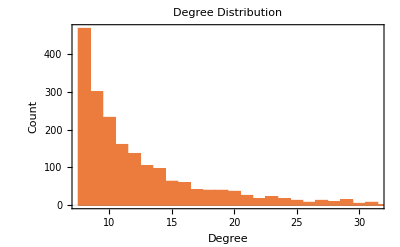
-Graphics-Min degree: 8
Max degree: 106
Mean degree: 13.21
Median degree: 10

```mathematica
degrees = VertexDegree[g];

Row[{
  Histogram[degrees, {1},
    PlotLabel -> "Degree Distribution",
    AxesLabel -> {"Degree", "Count"},
    PlotTheme -> "Scientific",
    ImageSize -> 400],
  Spacer[20],
  Column[{
    "Min degree: " <> ToString[Min[degrees]],
    "Max degree: " <> ToString[Max[degrees]],
    "Mean degree: " <> ToString[NumberForm[N[Mean[degrees]], 4]],
    "Median degree: " <> ToString[Median[degrees]]
  }]
}]
```

## 6. Centrality Analysis: Hubs and Bridges

While degree counts direct connections, betweenness centrality measures how often a vertex lies on the shortest path between other pairs of vertices. Artworks with high betweenness are semantic bridges — they connect otherwise distant parts of the graph. These tend to be works that combine elements from different artistic traditions, periods, or media, making them semantically intermediate between distinct clusters. Identifying these bridge artworks can reveal surprising connections: a print technique linking decorative arts to fine art, or a subject matter spanning centuries. The highlighted graph fades non-bridge artworks to make the bridge structure visible.

```mathematica
bc = BetweennessCentrality[g];
topBridgeIdx = Ordering[bc, -10];

Print[Style["Top 10 Bridge Artworks (highest betweenness centrality):", Bold]];
Grid[
  Prepend[
    Table[
      Module[{aid = graphIds[[idx]], meta = artworks[ToString[graphIds[[idx]]]]},
        {StringTake[meta["title"], UpTo[50]],
         StringJoin[Riffle[meta["types"], ", "]],
         NumberForm[bc[[idx]], 4]}],
      {idx, topBridgeIdx}],
    Style[#, Bold] & /@ {"Title", "Types", "Betweenness"}],
  Frame -> All, Alignment -> {{Left, Left, Center}}]
```

Top 10 Bridge Artworks (highest betweenness centrality):

Title | Types | Betweenness
Fotoreproductie van een schilderij, voorstellende  | reproductie, bladzijde, photograph | 24380.
Erat lux vera, quae illuminat omnem hominem venien | boekillustratie, print | 26580.
Gezicht op een kasteel | albumblad, print | 30130.
Rietgors zittend op een tak | print | 32120.
Studieblad met een man bij een mand en figuren | print | 36430.
Ziet in dit prentgestel verscheiden schetsen pronk | popular print, print | 49280.
Gezicht op verschillende daken | print | 55650.
Affiche van de Chambre Syndicale des Éditeurs et M | poster, print | 59180.
Portret van Voltaire | print | 61590.
Portret van Conradijn Cunaeus | photomechanical print | 67720.

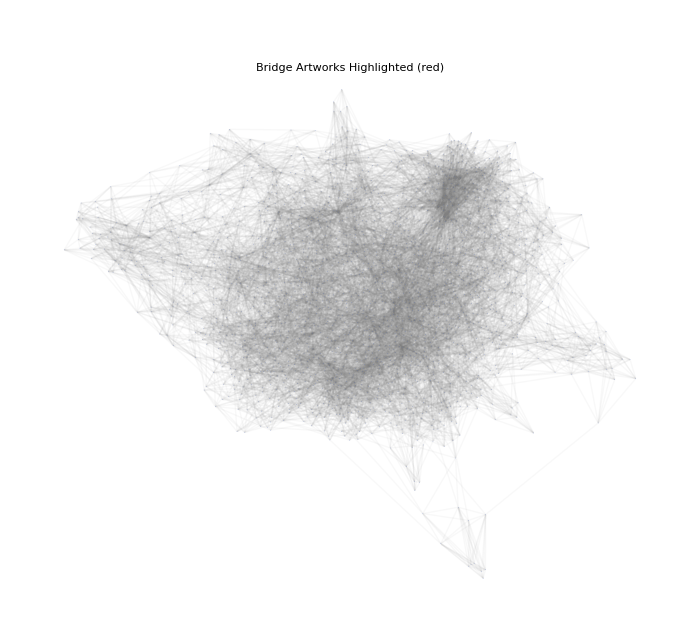

```mathematica
(* Highlight bridges on the graph *)
HighlightGraph[g,
  Style[#, Red, PointSize[0.02]] & /@ topBridgeIdx,
  GraphHighlightStyle -> "DehighlightFade",
  PlotLabel -> "Bridge Artworks Highlighted (red)",
  ImageSize -> 700]
```

## 7. Community Metadata Composition

A central question is whether the algorithmically discovered communities correspond to categories art historians would recognise, or whether the embedding model has found different semantic groupings. For each of the largest communities, we aggregate the object types and subjects of its members into bar charts. Communities dominated by a single type (e.g., photograph or print) confirm that the model captures traditional categorical distinctions. More interesting are communities that mix types but share subjects or techniques — these reveal affinities that cross formal boundaries, such as maritime-themed works spanning paintings, prints, and ship models.

Community 1 (10 works)

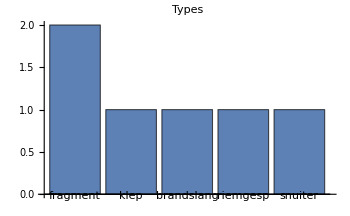
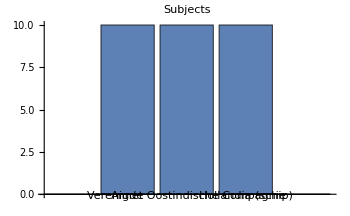

Community 2 (28 works)

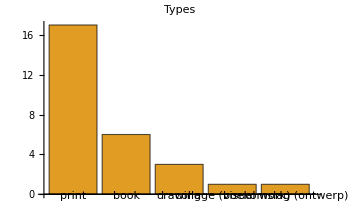
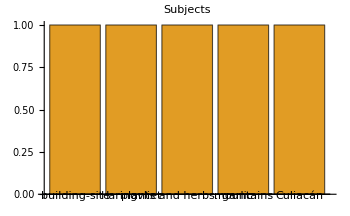

Community 3 (32 works)

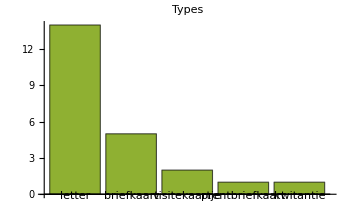
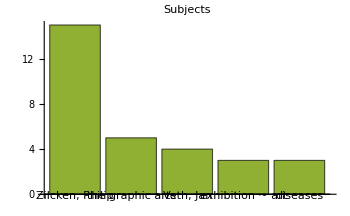

Community 4 (50 works)

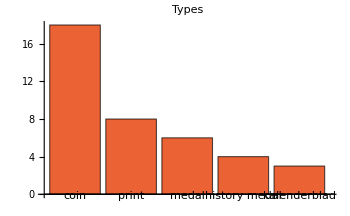
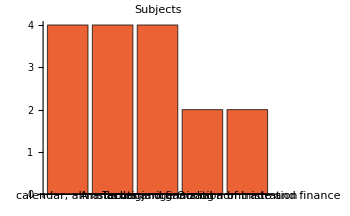

Community 5 (226 works)

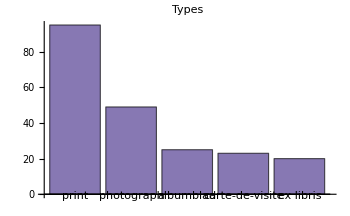
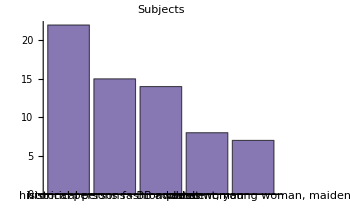

Community 6 (487 works)

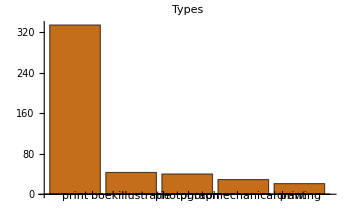
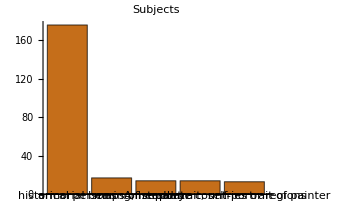

Community 7 (566 works)

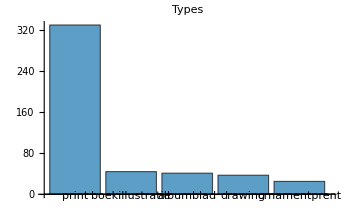
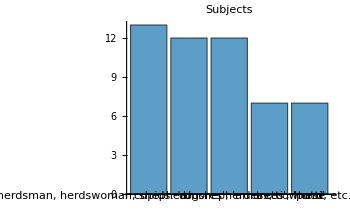

Community 8 (601 works)

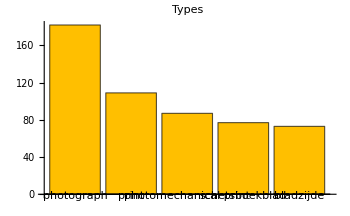
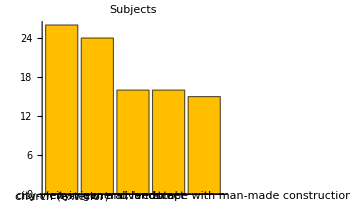

```mathematica
(* Metadata composition of largest communities *)
nShow = Min[8, Length[communities]];
bigComms = communities[[Ordering[Length /@ communities, -nShow]]];

Do[
  Module[{comm = bigComms[[ci]], memberIds, types, topTypes, subjects, topSubjects},
    memberIds = graphIds[[comm]];
    types = Flatten[Table[artworks[ToString[id]]["types"], {id, memberIds}]];
    subjects = Flatten[Table[artworks[ToString[id]]["subjects"], {id, memberIds}]];
    topTypes = TakeLargest[Counts[types], Min[5, Length[Counts[types]]]];
    topSubjects = TakeLargest[Counts[subjects], Min[5, Length[Counts[subjects]]]];
    Print[Style["Community " <> ToString[ci] <> " (" <> ToString[Length[comm]] <> " works)", 14, Bold]];
    Print[Row[{
      BarChart[Values[topTypes], ChartLabels -> Keys[topTypes],
        ImageSize -> 350, ChartStyle -> ColorData[97][ci],
        PlotLabel -> "Types"],
      Spacer[15],
      BarChart[Values[topSubjects], ChartLabels -> Keys[topSubjects],
        ImageSize -> 350, ChartStyle -> ColorData[97][ci],
        PlotLabel -> "Subjects"]
    }]]],
  {ci, nShow}]
```

## 8. Inter-Community Similarity

Each community can be summarised by its centroid — the average embedding of all its members, re-normalised to unit length. Cosine similarity between community centroids quantifies how semantically close or distant different communities are at the macro level. The resulting heatmap is a compact summary of the collection's large-scale structure: warm colours indicate semantically adjacent communities (perhaps historically related traditions), while cool colours mark communities in distant regions of embedding space. The community network graph connects communities whose similarity exceeds a threshold, with vertex size proportional to community size.

```mathematica
(* Community centroids *)
commCentroids = Table[
  Normalize[Mean[graphEmb[[comm]]]],
  {comm, communities}];
commSimMat = Outer[Dot, commCentroids, commCentroids, 1];

MatrixPlot[commSimMat,
  PlotLabel -> "Inter-Community Cosine Similarity",
  ColorFunction -> "TemperatureMap",
  PlotLegends -> Automatic,
  FrameLabel -> {"Community", "Community"},
  ImageSize -> 500]
```

-Graphics-

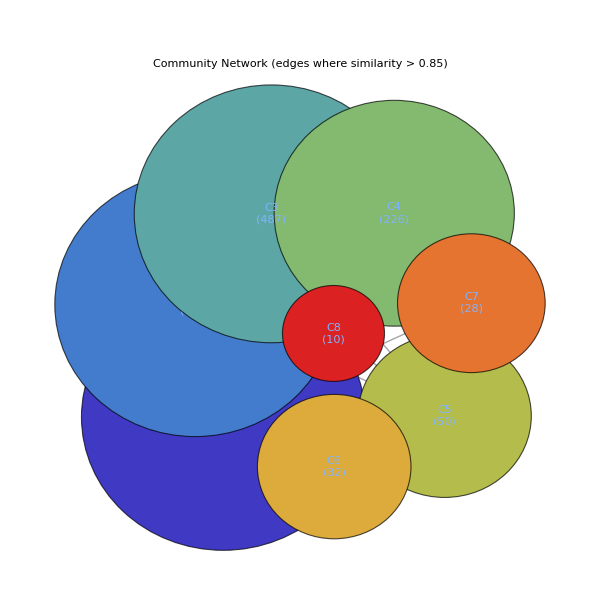

```mathematica
(* Community centroid network *)
commEdges = Flatten[Table[
  If[i < j && commSimMat[[i, j]] > 0.85,
    {Labeled[UndirectedEdge[i, j],
      NumberForm[commSimMat[[i, j]], 2]]},
    {}],
  {i, Length[communities]}, {j, Length[communities]}]];

commGraph = Graph[Range[Length[communities]], commEdges,
  VertexSize -> (Thread[Range[Length[communities]] ->
    Log[2, Length /@ communities] / 4]),
  VertexLabels -> Table[
    i -> Placed["C" <> ToString[i] <> "\n(" <> ToString[Length[communities[[i]]]] <> ")", Center],
    {i, Length[communities]}],
  VertexStyle -> (Thread[Range[Length[communities]] ->
    (ColorData["Rainbow"][#/Length[communities]] & /@ Range[Length[communities]])]),
  EdgeStyle -> Directive[Thick, Gray],
  GraphLayout -> "SpringEmbedding",
  PlotLabel -> "Community Network (edges where similarity > 0.85)",
  ImageSize -> 600]
```